```mathematica
SetDirectory[NotebookDirectory[]];
Needs["package`main`"];
```

There exists the unique tree.

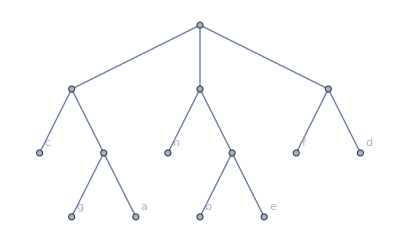

```mathematica
threeUPP["input/compatible_unique_1.txt"]
```

Not unique! There are two distinct trees.

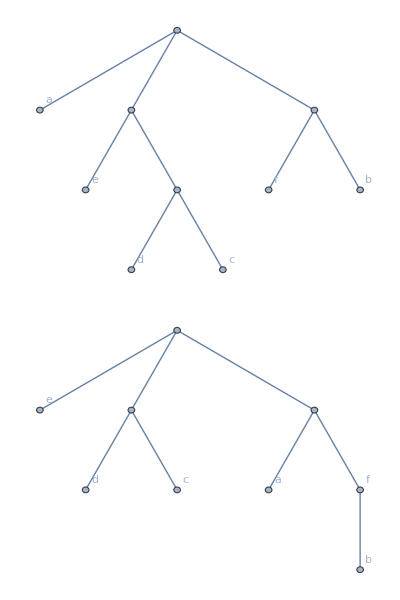

```mathematica
threeUPP["input/compatible_twoTrees.txt"]
```

```mathematica
characters = {{"acd","bef","g"},{"acg","bef","d"},{"ade","bcf","g"},{"ace","bfg","d"},{"abcd","eg","f"},{"acef","bd","g"},{"acf","bg","de"}};

threeUPP[characters]
```

Not compatible, the subset of characters {{acd, bef, g}, {ade, bcf, g}, {acf, bg, de}} is incompatible.

{{acd,bef,g},{ade,bcf,g},{acf,bg,de}}

```mathematica
characters ={{"abdf","c","e"},{"af","b","cde"},{"ae","bf","cd"},{"a","bf","cde"},{"abcf","d","e"},{"acde","b","f"},{"abf","ce","d"},{"a","bef","cd"},{"adef","b","c"},{"a","b","cdef"},{"abf","cd","e"}};


threeUPP[characters]
```

Not unique! There are two distinct trees.

-Graphics-